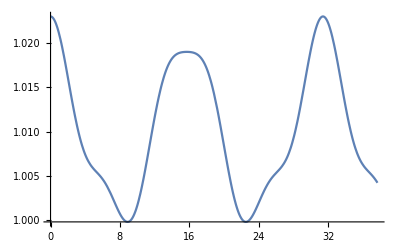

```mathematica
B0=1;B1c=0.1;B20=1+0.2 Cos[ϕ];B2c=0.1;ι=0.4;
B[r_,θ_,ϕ_]:=B0+r B1c Cos[θ]+r^2(B20+B2c Cos[2θ]);
Plot[B[0.1,ι ϕ,ϕ],{ϕ,0,12π}]
```

```mathematica
B[r_,θ_,ϕ_]=B0+r B1c Cos[θ]+r^2(B200+B201 Cos[ϕ]+B2c Cos[2θ]);
magnitudeB0squared=Chop@Integrate[B[r,θ,ϕ]^2,{r,0,a},{θ,0,2π},{ϕ,0,2π}]
```

2/15 a (30 B0^2+5 a^2 B1c^2+20 a^2 B0 B200+3 a^4 (2 B200^2+B201^2+B2c^2)) π^2

```mathematica
√magnitudeB0squared
```

√(2/15) √(a (30 B0^2+5 a^2 B1c^2+20 a^2 B0 B200+3 a^4 (2 B200^2+B201^2+B2c^2))) π

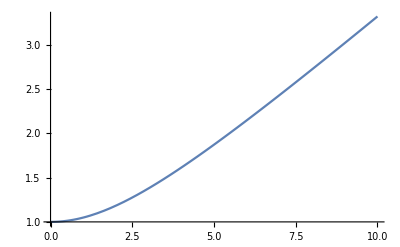

```mathematica
Plot[√(1+0.1 B1c^2),{B1c,0,10}]
```

```mathematica
(*TODO: Scale B1c by an amount and then scale delta=RMS(B20) by the volume average √(B^2) with the B1c scaling, similar to √(1+0.1 B1c^2)*)
```